```mathematica
(* calculating the complex reflectivity of a chirped FBG with parameters
based on results in Figure 1 of the reference {F. Ouellette, "Dispersion cancellation using linearly chirped
Bragg grating filters in optical waveguides" Optics Letters (1987)}.
Done by Spencer Jolly, B-PHOT Vrije Universiteit Brussel *)
```

```mathematica
ClearAll[F,kL,d,x,y,solution]
```

```mathematica
F=40*3.1415926;
```

```mathematica
kL=2*3.1415926;
```

```mathematica
solution=ParametricNDSolve[{y''[x]-I(2*d-F*x)*y'[x]-(kL^2)*y[x]==0,y'[-1/2]==kL*Exp[I*(-d-F/8)],y[1/2]==0},y,{x,-1/2,1/2},{d}]
```

{y→ParametricFunction[<>]}

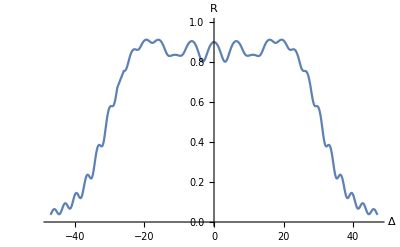

```mathematica
Plot[Evaluate[Abs[(y[d][-1/2]/.solution)]^2],{d,-47,47},PlotRange->{0,1},AxesLabel-> {Δ,R}]
```

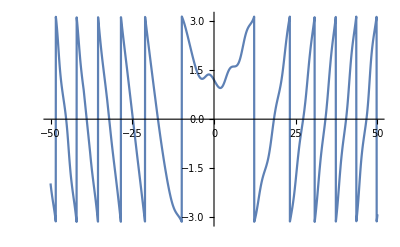

```mathematica
Plot[Evaluate[Arg[(y[d][-1/2]/.solution)]],{d,-50,50},PlotRange->{-3.1415926,+3.1415926}]
```